```mathematica
ClearAll[T,gamma,trs,trl,tl0,trg,g0,x, g0list1,g0list2,phi1,phi2,y1,y2]

g=g0(1-x/trg)^2;
q=1/(1+Exp[-(x-trq)/gammaq]);
s=1/(1+Exp[-(x-trs)/gammas]);
tl=tl0*(1-x/trl);
inoc=0.03;
```

```mathematica
tl0=30; (*Lagtime for no trehalose*)
trl=850; (*increasing this decreases growth rate for both*)
trs=800;
trg=1200;
trq=400;
gammaq=100;
gammas=25;
```

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]], PlotRange->All]&,{f,g}];{frange,grange}=(PlotRange/. AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

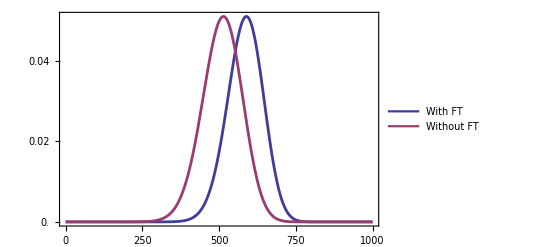

```mathematica
plot=TwoAxisPlot[{(inoc*s*g^(T-tl))/.g0->6/.T->20, (inoc*g^(T-tl))/.g0->6/.T->20}, {x,0,1000}];
Legended[plot,LineLegend[{ColorData[1][1],ColorData[1][2] },{"With FT","Without FT"}]]
```

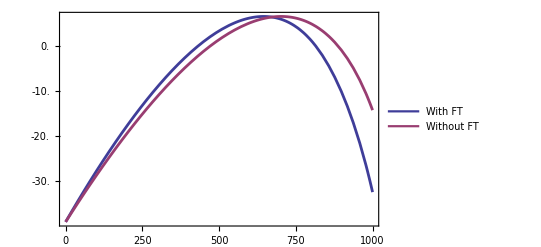

```mathematica
plot=TwoAxisPlot[{Log[(s*g^(T-tl))/.g0->10/.T->20], Log[(g^(T-tl))/.g0->10/.T->10]}, {x,0,1000}];
Legended[plot,LineLegend[{ColorData[1][1],ColorData[1][2] },{"With FT","Without FT"}]]
```

```mathematica
plot=Manipulate[TwoAxisPlot[{Log[(s*g^(T-tl))/.g0->10], Log[(inoc*g^(T-tl))/.g0->2]}, {x,0,1000}], {T,10,50}]
```

```mathematica
plot=Manipulate[TwoAxisPlot[{(inoc*s*g^(T-tl))/.g0->go, (inoc*g^(T-tl))/.g0->go}, {x,0,1000}], {go,2,50},{T,10,50}]
```

```mathematica
g0list={6,8,10,12,14};
Tlist={15,20,25};
```

```mathematica
eq=Simplify[D[s*g^(T-tl),x]];
```

```mathematica
eqd=D[eq,x];
```

```mathematica
NSolve[(eq/.T->15/.g0->2)==0,{x},PositiveReals]
```

{{x→494.365}}

```mathematica
Valuess of g0;
(*These are the phenotype values with freeze thaw*)

phi1=Flatten[{x/.NSolve[(eq/.T->Tlist[[1]]/.g0->g0list[[1]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eq/.T->Tlist[[1]]/.g0->g0list[[2]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eq/.T->Tlist[[1]]/.g0->g0list[[3]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eq/.T->Tlist[[1]]/.g0->g0list[[4]])==0,{x},PositiveReals][[1]],x/.NSolve[(eq/.T->Tlist[[1]]/.g0->g0list[[5]])==0,{x},PositiveReals][[1]]}]
phi2=Flatten[{x/.NSolve[(eq/.T->Tlist[[2]]/.g0->g0list[[1]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eq/.T->Tlist[[2]]/.g0->g0list[[2]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eq/.T->Tlist[[2]]/.g0->g0list[[3]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eq/.T->Tlist[[2]]/.g0->g0list[[4]])==0,{x},PositiveReals][[1]],x/.NSolve[(eq/.T->Tlist[[2]]/.g0->g0list[[5]])==0,{x},PositiveReals][[1]]}]
phi3=Flatten[{x/.NSolve[(eq/.T->Tlist[[3]]/.g0->g0list[[1]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eq/.T->Tlist[[3]]/.g0->g0list[[2]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eq/.T->Tlist[[3]]/.g0->g0list[[3]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eq/.T->Tlist[[3]]/.g0->g0list[[4]])==0,{x},PositiveReals][[1]],x/.NSolve[(eq/.T->Tlist[[3]]/.g0->g0list[[5]])==0,{x},PositiveReals][[1]]}]
y1=Transpose[{g0list,phi1}]
y2=Transpose[{g0list,phi2}]
y3=Transpose[{g0list,phi3}]
```

{644.889,674.744,695.635,711.387,723.875}

{588.966,621.738,644.931,662.535,676.534}

{533.989,569.067,594.103,613.246,628.56}

{{6,644.889},{8,674.744},{10,695.635},{12,711.387},{14,723.875}}

{{6,588.966},{8,621.738},{10,644.931},{12,662.535},{14,676.534}}

{{6,533.989},{8,569.067},{10,594.103},{12,613.246},{14,628.56}}

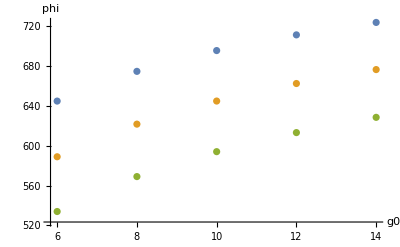

```mathematica
ListPlot[{y1,y2,y3}, AxesLabel->{g0,phi}, PlotRange->All]
```

```mathematica
eqnoft=D[inoc*g^(T-tl),x];
eqdnoft=D[eqnoft,x];
```

```mathematica
lgr=inoc*s*g^(T-tl);
lgrnoft=inoc*g^(T-tl);
```

```mathematica
(*Phenotype Values without freeze thaw*)
phi1noft=Flatten[{x/.NSolve[(eqnoft/.T->Tlist[[1]]/.g0->g0list[[1]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eqnoft/.T->Tlist[[1]]/.g0->g0list[[2]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eqnoft/.T->Tlist[[1]]/.g0->g0list[[3]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eqnoft/.T->Tlist[[1]]/.g0->g0list[[4]])==0,{x},PositiveReals][[1]],x/.NSolve[(eqnoft/.T->Tlist[[1]]/.g0->g0list[[5]])==0,{x},PositiveReals][[1]]}]
phi2noft=Flatten[{x/.NSolve[(eqnoft/.T->Tlist[[2]]/.g0->g0list[[1]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eqnoft/.T->Tlist[[2]]/.g0->g0list[[2]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eqnoft/.T->Tlist[[2]]/.g0->g0list[[3]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eqnoft/.T->Tlist[[2]]/.g0->g0list[[4]])==0,{x},PositiveReals][[1]],x/.NSolve[(eqnoft/.T->Tlist[[2]]/.g0->g0list[[5]])==0,{x},PositiveReals][[1]]}]
phi3noft=Flatten[{x/.NSolve[(eqnoft/.T->Tlist[[3]]/.g0->g0list[[1]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eqnoft/.T->Tlist[[3]]/.g0->g0list[[2]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eqnoft/.T->Tlist[[3]]/.g0->g0list[[3]])==0,{x},PositiveReals][[1]],
x/.NSolve[(eqnoft/.T->Tlist[[3]]/.g0->g0list[[4]])==0,{x},PositiveReals][[1]],x/.NSolve[(eqnoft/.T->Tlist[[3]]/.g0->g0list[[5]])==0,{x},PositiveReals][[1]]}]
phi1noft=If[#==1000,0,#]&/@phi1noft
phi2noft=If[#==1000,0,#]&/@phi2noft
phi3noft=If[#==1000,0,#]&/@phi3noft
y1noft=Transpose[{g0list,phi1noft}]
y2noft=Transpose[{g0list,phi2noft}]
y3noft=Transpose[{g0list,phi3noft}]
```

{575.991,614.111,641.225,661.937,678.513}

{514.127,554.388,583.1,605.075,622.692}

{454.571,496.873,527.105,550.283,568.888}

{575.991,614.111,641.225,661.937,678.513}

{514.127,554.388,583.1,605.075,622.692}

{454.571,496.873,527.105,550.283,568.888}

{{6,575.991},{8,614.111},{10,641.225},{12,661.937},{14,678.513}}

{{6,514.127},{8,554.388},{10,583.1},{12,605.075},{14,622.692}}

{{6,454.571},{8,496.873},{10,527.105},{12,550.283},{14,568.888}}

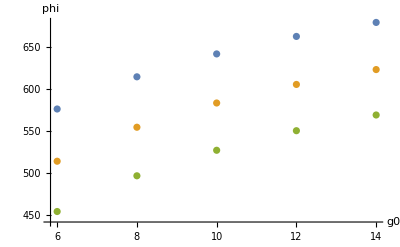

```mathematica
ListPlot[{y1noft,y2noft, y3noft}, AxesLabel->{g0,phi}, PlotRange->All]
```

```mathematica
{lgrnoft/.T->Tlist[[1]]/.x->phi1[[1]]/.g0->g0list[[1]],lgrnoft/.T->Tlist[[1]]/.x->phi1noft[[1]]/.g0->g0list[[1]]}
{lgr/.T->Tlist[[1]]/.x->phi1[[1]]/.g0->g0list[[1]],lgr/.T->Tlist[[1]]/.x->phi1noft[[1]]/.g0->g0list[[1]]}
```

{0.20871,0.395494}

{0.00897781,0.00443123}

```mathematica
points1={}; (*normal conditions, {Evo, WT}*)
points2={}; (*FT, {Evo, WT}*)
points3={};
points4={};
points5={};
points6={};
For[i=1,i<6,i++,AppendTo[points1,{Log[lgrnoft/.T->Tlist[[1]]/.x->phi1[[i]]/.g0->g0list[[i]]],Log[lgrnoft/.T->Tlist[[1]]/.x->phi1noft[[i]]/.g0->g0list[[i]]]}]]
For[i=1,i<6,i++,AppendTo[points2,{Log[lgr/.T->Tlist[[1]]/.x->phi1[[i]]/.g0->g0list[[i]]],Log[lgr/.T->Tlist[[1]]/.x->phi1noft[[i]]/.g0->g0list[[i]]]}]]
For[i=1,i<6,i++,AppendTo[points3,{Log[lgrnoft/.T->Tlist[[2]]/.x->phi2[[i]]/.g0->g0list[[i]]],Log[lgrnoft/.T->Tlist[[2]]/.x->phi2noft[[i]]/.g0->g0list[[i]]]}]]
For[i=1,i<6,i++,AppendTo[points4,{Log[lgr/.T->Tlist[[2]]/.x->phi2[[i]]/.g0->g0list[[i]]],Log[lgr/.T->Tlist[[2]]/.x->phi2noft[[i]]/.g0->g0list[[i]]]}]]
For[i=1,i<6,i++,AppendTo[points5,{Log[lgrnoft/.T->Tlist[[3]]/.x->phi3[[i]]/.g0->g0list[[i]]],Log[lgrnoft/.T->Tlist[[3]]/.x->phi3noft[[i]]/.g0->g0list[[i]]]}]]
For[i=1,i<6,i++,AppendTo[points6,{Log[lgr/.T->Tlist[[3]]/.x->phi3[[i]]/.g0->g0list[[i]]],Log[lgr/.T->Tlist[[3]]/.x->phi3noft[[i]]/.g0->g0list[[i]]]}]]
```

```mathematica
points1
points2
points3
points4
points5
points6
```

{{-1.56681,-0.927621},{0.257753,0.80216},{1.92873,2.39963},{3.44652,3.85832},{4.82957,5.19287}}

{{-4.713,-5.41908},{-2.32587,-2.93963},{-0.275479,-0.816795},{1.51731,1.03576},{3.10972,2.67874}}

{{1.26036,1.9754},{3.89068,4.5264},{6.20064,6.77557},{8.25066,8.77592},{10.0915,10.5747}}

{{-2.97491,-3.74535},{0.297536,-0.393158},{3.05525,2.42458},{5.43935,4.85735},{7.54088,7.0001}}

{{4.99832,5.7649},{8.46599,9.16005},{11.4374,12.078},{14.0356,14.6335},{16.3453,16.9076}}

{{-0.326781,-1.14469},{3.83751,3.09519},{7.30335,6.61582},{10.2769,9.63241},{12.8846,12.2756}}

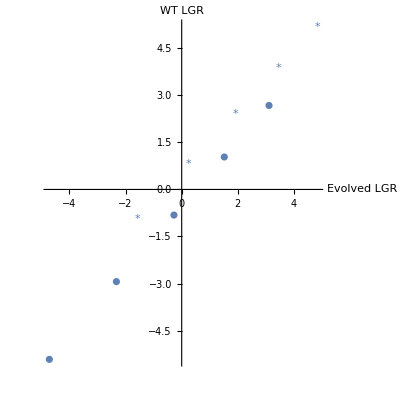

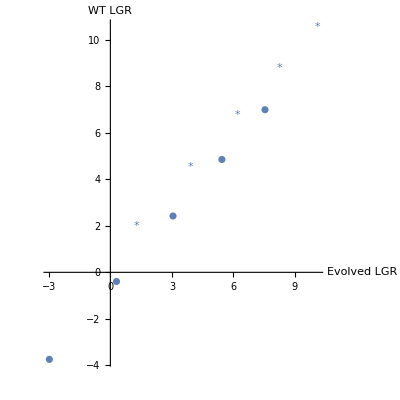

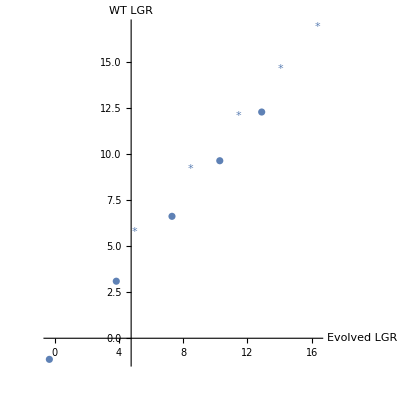

```mathematica
plot1=ListPlot[{points1}, AxesLabel->{"Evolved LGR", "WT LGR"}, PlotMarkers->"*"];
plot2=ListPlot[{points2}, AxesLabel->{"Evolved LGR", "WT LGR"}];
plot3=ListPlot[{points3}, AxesLabel->{"Evolved LGR", "WT LGR"},PlotMarkers->"*"];
plot4=ListPlot[{points4}, AxesLabel->{"Evolved LGR", "WT LGR"}];
plot5=ListPlot[{points5}, AxesLabel->{"Evolved LGR", "WT LGR"}, PlotMarkers->"*"];
plot6=ListPlot[{points6}, AxesLabel->{"Evolved LGR", "WT LGR"}];
Show[{plot1,plot2}, PlotRange->All, AspectRatio->1]
Show[{plot3,plot4}, PlotRange->All, AspectRatio->1]
Show[{plot5,plot6}, PlotRange->All, AspectRatio->1]
```

```mathematica
BarLegend[{"SolarColors",{1,5}}]

BarLegend[{"AvocadoColors",{1,5}}]

BarLegend[{"LakeColors",{1,5}}]
```